## Computation for Figure 8.6 and 8.7: Obtain a semianalytic solution for Θ_0+Ψ and Θ_1 at recombination by carrying out the integrals Eq.8.24 and .8.26.

```mathematica
Quit[]
```

```mathematica
(*Needs["Dodelson`LocalFunctions`"]
*)
Needs["Dodelson`CommonParameters`"]
Needs["Dodelson`DodelsonDefine`"]
equalitySubs
ayetaSubs
EnergyDenSubs
SoundSubs
```

General::obspkg: TraditionalForm`"Utilities`Notation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Needs::nocont: Context TraditionalForm`"Dodelson`CommonParameters`" was not created when Needs was evaluated.

Needs::nocont: Context TraditionalForm`"Dodelson`DodelsonDefine`" was not created when Needs was evaluated.

Some definitions referencing 'equality' point :

defkeq :: k_eq→a_eq H(a_eq)

subkeq :: k_eq→√2 √((H_0^2 Ω_m)/a_eq)

subH0 :: H_0→(√((a_eq k_eq^2)/Ω_m))/(√2)

subkkeq :: k→k_eq kk_eq

subetat :: η'(t)→1/(a(η))

subyeta :: y(η)→(a(η))/a_eq

subDyeta :: y'(η)→(a'(η))/a_eq

subHt :: H→(a'(t))/(a(t))

defaeta :: a(η_):=y(η) a_eq

subHeta :: H→(a'(η))/(a(η))^2

deffnu :: f_ν:=ρ_ν/(ρ_γ+ρ_ν)

defRhoG :: ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoRad :: ρ_r(a_):=(ρ_γ(a))/(1-f_ν)

defRhoB :: ρ_b(a_):=(Ω_b ρ_cr)/a^3

defRhoM :: ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoDE :: ρ_de(a_):=(Ω_de ρ_cr)/a^3

defRho :: ρ(a_):=ρ_de(a)+ρ_m(a)+ρ_r(a)

defOmegaM :: Ω_m:=Ω_b+Ω_dm

subRhoCR :: ρ_cr→(3 H_0^2)/(8 G π)

defe255 :: (∂ρ_t(t))/(∂t)+(3 (∂a_t(t))/(∂t) (𝒫_t(t)+ρ_t(t)))/(a_t(t))==0

defe255a :: (∂ρ_a(a))/(∂a)+(3 (𝒫_a(a)+ρ_a(a)))/a==0

subaeq :: a_eq→-C_γ/((f_ν-1) h^2 Ω_m)

subC :: C_γ→-a_eq (f_ν-1) h^2 Ω_m

defHa :: Ha(a_):=√(1/3 (8 π G) ρ(a))

defetade :: η_de(a_):=∫_0^a 1/(aa^2 Ha(aa))ⅆaa

defe242 :: χ(a_):=∫_a^1 1/(aa^2 Ha(aa))ⅆaa

For backward consistency : Null

η[a_] :: (2 (√(a+a_eq)-√a_eq))/(H_0 √Ω_m)

η_* :: (2 (√(a_eq+a_*)-√a_eq))/(H_0 √Ω_m)

η_y[y_] :: (2 (√(y a_eq+a_eq)-√a_eq))/(H_0 √Ω_m)

Jacobian dη/dy => a_eq/(H_0 √(a_eq (y+1)) √Ω_m)
Or  -> dη/dy = (√2)/(k_eq √(y+1))

y[η_] :: 1/8 k_eq η (k_eq η+4 √2)

Useful relationships: From the definitions: dη==dt/a  and  H=((∂a(t))/(∂t))/(a(t)) => a H==(∂a(t))/(∂t) => dt==da/(a H) => dη==da/(a^2 H)

defR :: R(a_):=(3 ρ_b(a))/(4 ρ_γ(a))

defReta :: R_η(η_):=(3 ρ_b(y(η) a_eq))/(4 ρ_γ(y(η) a_eq))

Eqn819 :: c_s(a_):=√(1/(3 (R(a)+1)))

Eqn819eta :: c_s(eta_):=√(1/(3 (R_η(eta)+1)))

Eqn822 :: r_s(η_):=∫_0^η c_s(ep)ⅆep

c_s(eta_):=√(1/(3 (R_η(eta)+1))) => 1/(√3 √(1-(3 k_eq η (k_eq η+4 √2) Ω_b)/(32 (f_ν-1) Ω_m)))Null

r_s[η_] :: -1/(3 √f_b k_eq)4 √2 √(1-f_ν) (log((4 √6 √f_b)/(√(1-f_ν))-(6 √2 f_b)/(f_ν-1))-log((√3 √f_b √(32-(3 f_b k_eq η (k_eq η+4 √2))/(f_ν-1)))/(√(1-f_ν))-(3 f_b (k_eq η+2 √2))/(f_ν-1)))

#### Check sound horizon calculation, Eqn.8.22

```mathematica
Eqn822//ReleaseHold
Eqn819eta//ReleaseHold
defReta//ReleaseHold
defR//ReleaseHold
Print[
Eqn822,"
",
Eqn819eta,"
",
defReta," => ",
Subscript[R, η][η]/.subC/.subrhocr//PowerExpand//Simplify,"
R as function of a :  ",
defR," => ",
R[a]," => ",R[a]/.subC,"
 => ",R[y Subscript[a, eq]]," => ",R[y Subscript[a, eq]]/.subC
];
```

r_s(η_):=∫_0^η c_s(ep)ⅆep
c_s(eta_):=√(1/(3 (R_η(eta)+1)))
R_η(η_):=(3 ρ_b(y(η) a_eq))/(4 ρ_γ(y(η) a_eq)) => -(3 k_eq η (k_eq η+4 √2) Ω_b)/(32 (f_ν-1) Ω_m)
R as function of a :  R(a_):=(3 ρ_b(a))/(4 ρ_γ(a)) => (3 a h^2 Ω_b)/(4 C_γ) => -(3 a Ω_b)/(4 a_eq (f_ν-1) Ω_m)
 => (3 a_eq h^2 y Ω_b)/(4 C_γ) => -(3 y Ω_b)/(4 (f_ν-1) Ω_m)

```mathematica
(*Aside*)
Print["The definition for R is R==3/4(SubscriptBox[ρ, b][a])/(SubscriptBox[ρ, γ][a]) . 
'equality' for a_eq is defined in terms of matter-radiation equality or matter(baryon+dark)-radiation(photon+neutrino) equality.  We compute  R composed from baryon-photon ratios  ",
tmp=(R^bg)[a]==3/4(Subscript[ρ, b][a])/(Subscript[ρ, γ][a])/.Subscript[ρ, b][a]->Subscript[Ω, b] Subscript[ρ, cr]/a^3," 
which is ",tmp/.a->1," 
For Dodelson normalization  :  ",subaeq,"
For HS normalization  : ",a->Subscript[a, HS]/Subscript[a, 0],"=>",Subscript[a, eq]->Subscript[a, HSeq]/Subscript[a, 0],"=>",Subscript[a, 0]->1/Subscript[a, eq],"
",tmp=tmp/.a->Subscript[a, HS]/Subscript[a, 0],"
",tmp=tmp/.Subscript[a, 0]->1/Subscript[a, eq],"
",tmp=tmp/.subaeq,"  <= This is HS's D8,  where Ω_0->Ω_m approximately.
What is HS's R_eq?  R_eq ==R[a_HSeq->1]?    ",
tmp/.Subscript[a, HS]->1/.R->Subscript[R, eq]
," <= This is compatible with D8."];
```

The definition for R is R==3/4(SubscriptBox[ρ, b][a])/(SubscriptBox[ρ, γ][a]) . 
'equality' for a_eq is defined in terms of matter-radiation equality or matter(baryon+dark)-radiation(photon+neutrino) equality.  We compute  R composed from baryon-photon ratios  R^bg[a]==(3 a h^2 Ω_b)/(4 C_γ) 
which is R^bg[1]==(3 h^2 Ω_b)/(4 C_γ) 
For Dodelson normalization  :  a_eq→-C_γ/((f_ν-1) h^2 Ω_m)
For HS normalization  : a→a_HS/a_0=>a_eq→a_HSeq/a_0=>a_0→1/a_eq
R^bg[a_HS/a_0]==(3 h^2 Ω_b a_HS)/(4 a_0 C_γ)
R^bg[a_eq a_HS]==(3 a_eq h^2 Ω_b a_HS)/(4 C_γ)
R^bg[-(a_HS C_γ)/((f_ν-1) h^2 Ω_m)]==-(3 Ω_b a_HS)/(4 (f_ν-1) Ω_m)  <= This is HS's D8,  where Ω_0->Ω_m approximately.
What is HS's R_eq?  R_eq ==R[a_HSeq->1]?    R_eq^bg[-C_γ/((f_ν-1) h^2 Ω_m)]==-(3 Ω_b)/(4 (f_ν-1) Ω_m) <= This is compatible with D8.

```mathematica
(*check consistency with Hu-Sugiyama D9*)
Print["Our expression for : ",
tmp=η->η[a]," => ",
tmp=tmp/.subrhocr;" => ",
tmp=tmp//PowerExpand//Simplify," => ",
" with : ",subkeq," => ",tmp1=subkeq,"
",tmp1=tmp[[1]]tmp1[[1]]->tmp[[2]]tmp1[[2]]//PowerExpand//Simplify,"
Consistent with D9+ "
];
subeta=tmp1[[1]]/Subscript[k, eq]->tmp1[[2]]/Subscript[k, eq]
```

Our expression for : η→(2 (√(a+a_eq)-√a_eq))/(H_0 √Ω_m) =>  => η→(2 (√(a+a_eq)-√a_eq))/(H_0 √Ω_m) =>  with : k_eq→√2 √((H_0^2 Ω_m)/a_eq) => k_eq→√2 √((H_0^2 Ω_m)/a_eq)
k_eq η→(2 √2 (√(a+a_eq)-√a_eq))/(√a_eq)
Consistent with D9+

η→(2 √2 (√(a+a_eq)-√a_eq))/(√a_eq k_eq)

(*Does our r_s match with H-S Fig.5 ?*)

subZrecomb :: z_*→1000

subarecomb :: a_*→1/(z_*+1)

subyrecomb :: y_*→(a_*)/a_eq

The k_1=π/r_s[η_*] = 5.82756  Is this close to 6.0 in Sugiyama Fig.5?

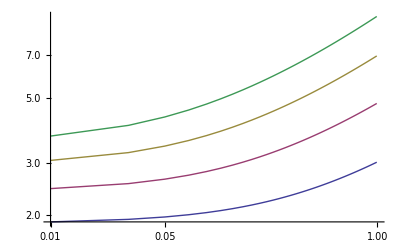

This is similar to Sugiyama Fig.5.

```mathematica
Print["(*Does our r_s match with H-S Fig.5 ?*)"]
subOm={Subscript[f, b]->(Subscript[Ω, b]/Subscript[Ω, m]),Subscript[Ω, m]->(1-Subscript[C, γ]/(h^2(1-Subscript[f, ν])))};
rsstar=Subscript[r, s][SubStar[η]] sec2Mpc//NumericalValues;
(* Take Subscript[Ω, 0]->1 *)
Print["The k_1=π/r_s[η_*] = ",100 π/rsstar/.Subscript[Ω, b]->1/.h->.7,"  Is this close to 6.0 in Sugiyama Fig.5? "
];
Table[
{  OO,100 π/(rsstar/.Subscript[Ω, b]->OO/.h->HH//PowerExpand)   }
,{HH,.4,1,.2}
,{OO,.01,1,.02}
];
ListLogLogPlot[ %,Joined->True]
Print["This is similar to Sugiyama Fig.5."]
```

#### Let's plot H-S Fig.5 from their definitions, around D9

r_(s.HS)(R_)→(2 √(2/3) log((√(R+1)+√(R+R_eq))/(R_eq^(1/2)+1)) √(R_eq^-1))/k_eq

r_(s.HS)(R_)→(4 √2 √(-((f_ν-1) Ω_m)/Ω_b) log((√(R+1)+√(R-(3 Ω_b)/(4 (f_ν-1) Ω_m)))/(1/2 √3 √(-Ω_b/((f_ν-1) Ω_m))+1)))/(3 k_eq)

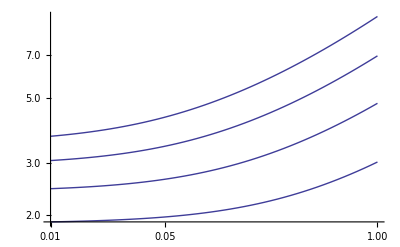

```mathematica
Clear[subOm]
D9=Subscript[r, s.HS][R_]->2/(3 Subscript[k, eq])√(6/Subscript[R, eq])Log[(√(1+R)+√(R+Subscript[R, eq]))/(1+√Subscript[R, eq])]
defR//ReleaseHold;
D9=D9/.Subscript[R, eq]->R[ Subscript[a, eq]]/.subC
rstmp[y_]:=D9[[2]]/.R->R[y Subscript[a, eq]]/.subC
subOm={Subscript[f, b]->(Subscript[Ω, b]/Subscript[Ω, m]),Subscript[Ω, m]->(1-Subscript[C, γ]/(h^2(1-Subscript[f, ν])))};
invrs=100 π/rstmp[y[SubStar[η]]]/sec2Mpc//NumericalValues;
LogLogPlot[Table[invrs/.h->hh/.Subscript[Ω, b]->OO,{hh,.4,1,.2}],{OO,.01,1}]
```

The formula for r_snear D9 reproduces Fig.5.

```mathematica
Print["Determine the meaning of coordinates of Fig.8.6 with only the Cos[k r_s[η_*] term when ",
subOm={Subscript[f, b]->(Subscript[Ω, b]/Subscript[Ω, m]),Subscript[Ω, m]->(1-Subscript[C, γ]/(h^2(1-Subscript[f, ν]))),Subscript[Ω, b]->.015/h^2,h->.7},
".
In Fig.8.6 the x-axis variable is x = k η_0,   where : ",
Subscript[η, 0]," => ", Subscript[η, 0] sec2Mpc//NumericalValues,"(Mpc)  and η_*==",SubStar[η] sec2Mpc//NumericalValues,"(Mpc).   Then, in the plot the value of  ",k Subscript[η, 0] ," for the third peak, k r_s[η_*] == 2π,  appears at k η_0 == 550  => ",k-> 550/Subscript[η, 0]," => ",tmpk=550/(Subscript[η, 0] sec2Mpc)//NumericalValues,"
Is this close to a 2π == k r_s[η_*]? => ",
tmp2=2π == k Subscript[r, s][SubStar[η]]  sec2Mpc//NumericalValues," => ",tmpk2=Solve[tmp2,k][[1]]
];
Print[" NOT at the third peak in Fig.8.6. ",tmpk," vs. ",tmpk2[[1,2]]," ratio ->",tmpk/tmpk2[[1,2]]
];
```

Determine the meaning of coordinates of Fig.8.6 with only the Cos[k r_s[η_*] term when {f_b→Ω_b/Ω_m,Ω_m→1-C_γ/((1-f_ν) h^2),Ω_b→0.015/h^2,h→0.7}.
In Fig.8.6 the x-axis variable is x = k η_0,   where : η_0 => 8506.83(Mpc)  and η_*==203.616(Mpc).   Then, in the plot the value of  k η_0 for the third peak, k r_s[η_*] == 2π,  appears at k η_0 == 550  => k→550/η_0 => 0.0646539
Is this close to a 2π == k r_s[η_*]? => 2 π==108.499 k => {k→0.0579098}

NOT at the third peak in Fig.8.6. 0.0646539 vs. 0.0579098 ratio ->1.11646

#### Supposedly, Fig.8.6 plots Eq.8.24 which we attempt to reproduce. Eqn.8.22, the sound horizon. We see that the Cos term alone is similar to Fig.8.6.

Cos[k r_s[η_*]]

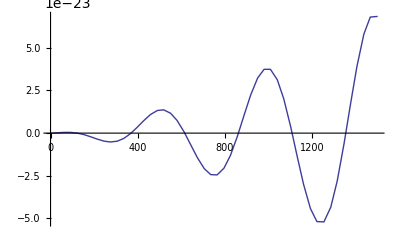

```mathematica
(*Let's look at Cos[k Subscript[r, s]] *)
tmp="Cos[k r_s[η_*]]"
SubStar[η];
tmp//ToExpression;
k[keta0_]:=keta0/Subscript[η, 0] //NumericalValues
krs[keta0_]:=(k[keta0] Subscript[r, s][SubStar[η]]//NumericalValues)
Plot[ k[keta0]^(3/2)  Cos[krs[keta0]],{keta0,0,1500}]
```

#### We investigate the integral term of Eqn.8.24.

```mathematica
DefEqn886
Φ[kkeq_,η_]:=Subscript[Φ, y][kkeq,y[η]]
Ψ[kkeq_,η_]:=Subscript[Ψ, y][kkeq,y[η]]
defe824=
"Θ_0[kkeq,η]+Φ[kkeq,η] == ( Θ_0[0]+Φ[0] ) Cos[k_eq kkeq  r_s[η]] + Integrate[integrand824[η,eta,kkeq],{eta,0,η}]"
e824Int=StringJoin[ "XIntegrate",StringSplit[defe824,{"==","Integrate" } ][[3]] ]
defint824="integrand824[η_,eta_,kkeq_]:=(kkeq SubscriptBox[k, eq])/(√3)(Φ[kkeq,eta]-Ψ[kkeq,eta]) Sin[ k_eq kkeq( r_s[η]-r_s[eta]) ]"
ToExpression[defint824];
```

Θ_0[kkeq,η]+Φ[kkeq,η] == ( Θ_0[0]+Φ[0] ) Cos[k_eq kkeq  r_s[η]] + Integrate[integrand824[η,eta,kkeq],{eta,0,η}]

XIntegrate[integrand824[η,eta,kkeq],{eta,0,η}]

integrand824[η_,eta_,kkeq_]:=(kkeq SubscriptBox[k, eq])/(√3)(Φ[kkeq,eta]-Ψ[kkeq,eta]) Sin[ k_eq kkeq( r_s[η]-r_s[eta]) ]

Reduce number of integration variables:

{eta→etakeq/k_eq,η→ηkeq/k_eq}

{f_b→Ω_b/Ω_m,Ω_m→1-C_γ/((1-f_ν) h^2),Ω_b→0.015/h^2,h→0.7}

For Fig.8.6 : k η_0 ranges to : 1500 or k ranges from 0 to 1500/η_0 => 1.71437×10^-15
The value of k_eq is : 3.48031×10^-16
So kkeq ranges from 0 to {0,4.92592}
and η_* k_eq = 7.28866

{ηkeq→7.28866,Φ(0)→1}

0.0250224

Power::infy: Infinite expression TraditionalForm`1/0^2 encountered.

∞::indet: Indeterminate expression TraditionalForm`0\ ComplexInfinity/etakeq^3\ « 1 » « 1 » (« 6 »^2 + « 18 »\ « 6 » + 8.) encountered.

NIntegrate::inumr: The integrand TraditionalForm`Indeterminate has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`etakeq near TraditionalForm`{etakeq} = TraditionalForm`{4.34959×10^-6}. NIntegrate obtained TraditionalForm`0.034973245964572026` and TraditionalForm`0.00006004582390843485` for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`etakeq near TraditionalForm`{etakeq} = TraditionalForm`{4.34959×10^-6}. NIntegrate obtained TraditionalForm`-0.0360604 and TraditionalForm`0.000027981504743326977` for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`etakeq near TraditionalForm`{etakeq} = TraditionalForm`{4.34959×10^-6}. NIntegrate obtained TraditionalForm`0.016725131507199318` and TraditionalForm`0.00003115068720398604` for the integral and error estimates.

General::stop: Further output of TraditionalForm`NIntegrate :: "ncvb" will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

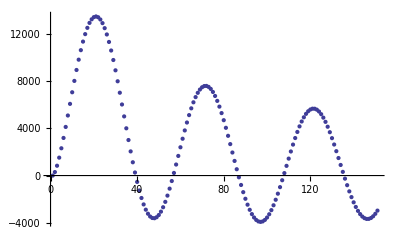

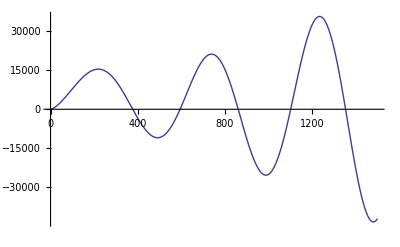

```mathematica
"Reduce number of integration variables: "
subIntvar={eta->etakeq/Subscript[k, eq],η->ηkeq/Subscript[k, eq]}
e824=ToExpression[e824Int]/.subIntvar//Simplify;
e824[[2]]={etakeq,10^-2,ηkeq};  (****)
e824[[1]]=e824[[1]]/Subscript[k, eq]/.kkeq->kkeq[keta0];
subOm
e824//NumericalValues;
Print["For Fig.8.6 : k η_0 ranges to : ",xmax=1500," or k ranges from 0 to ",xmax/Subscript[η, 0]," => ",xmax/Subscript[η, 0]//NumericalValues,"
The value of k_eq is : ",keq=Subscript[k, eq]//NumericalValues,"
So kkeq ranges from 0 to ",rangekkeq={0,xmax/Subscript[η, 0]/Subscript[k, eq]//NumericalValues },"
and η_* k_eq = ",SubStar[η] Subscript[k, eq]//NumericalValues
];
k[keta0_]:=keta0/Subscript[η, 0] //NumericalValues
krs[keta0_]:=k[keta0] Subscript[r, s][SubStar[η]]//NumericalValues
kkeq[keta0_]:=k[keta0]/Subscript[k, eq]//NumericalValues
subs={ηkeq->SubStar[η] Subscript[k, eq]//NumericalValues,Φ[0]->1}
i824=(e824//NumericalValues);

i824/.subs/.keta0->850/.XIntegrate->NIntegrate
tmp=i824/.subs;
tmp[[2]]={etakeq,10^-6,tmp[[2,3]]};

tab824=Table[keta0^(3/2)  (tmp/.XIntegrate->NIntegrate),{keta0,0,1500,10}];
ListPlot[tab824]

Plot[ keta0^(3/2) ( -.7 Cos[krs[keta0]]+(tmp/.XIntegrate->NIntegrate)),{keta0,0,1500}](* Cos coefficient unknown *)
```

```mathematica
eqn824[kkeq_,xaeq_,xy_]:=Module[{tmp,sub,zz,tmpXX },
sub={aeq->xaeq,Φ[0]->Phi0,Subscript[Θ, 0][0]->Theta0,keq->xkeqInvMpc,y->xy};
tmp=(Subscript[Θ, 0][0]+Φ[0])Cos[keq kkeq rsy]/.sub;
tmpXX=
1/(√3)NIntegrate[intgZ0[zz,Max[kkeq,minkkeq],xaeq,xy]/.sub ,{zz,Xmin,xy}];
Print["kkeq = ",kkeq,"     xaeq = ",xaeq,"  xy = ",xy,"  tmpXX = ",tmpXX,"tmp= ",tmp];
tmp+=tmpXX;
tmp]

Phi0=10^-6;
Theta0=Phi0;
keta0[k_]:=1000 k  +minkkeq
Do[
{Print[{keta0[k],eqn824[(k+minkkeq)/xkeqInvMpc,xaeq0,SubStar[y]] } ],
Print[Φ[keta0[k],Xmin]]},{k,0,1}]
tmp=Limit[Φ[kkeq,y],{y->0}]
Print["There are a number of inconsistencies -> When we take the limit of y->0 or η->0 of Φ[kkeq,y] we do not get Φ[0] but -> ",tmp];
Limit[Φ[kkeq,y],{kkeq->0}]
Limit[%,{y->0}]
rsy/.y->0//PowerExpand//Simplify
%//FullSimplify
```